# Digital Research Methods 13A: JSTOR Data for Research

## William J Turkel, wturkel@uwo.ca History 2816 / Digital Humanities 2130 / History 9877

## Citations for articles with ‘Darwin’ in the title

Ordinarily we request information directly from the JSTOR Data for Research site

http://about.jstor.org/service/data-for-research

Here we are using a small subset of the data that I archived on Github so our results would be reproducible

```mathematica
jstorCitations=Import["https://raw.githubusercontent.com/williamjturkel/Digital-Research-Methods/master/jstor-citations/citations.xml"];
```

Data are imported in Mathematica’s internal XML format

```mathematica
Short[jstorCitations,20]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Encoding→UTF-8]},XMLElement[citations,{},{XMLElement[article,{id→10.2307/20537402},{XMLElement[doi,{},{10.2307/20537402}],XMLElement[title,{},{Introduction: Darwin and the Evolution of Victorian Studies}],XMLElement[author,{},{Jonathan Smith}],XMLElement[journaltitle,{},{Victorian Studies}],XMLElement[volume,{},{51}],XMLElement[issue,{},{2}],XMLElement[pubdate,{},{2009-01-01T00:00:00Z}],XMLElement[pagerange,{},{pp. 215-221}],XMLElement[publisher,{},{Indiana University Press}],XMLElement[type,{},{fla}],XMLElement[reviewed-work,{},{}],XMLElement[abstract,{},{}]}],«924»,XMLElement[article,{id→10.2307/2405834},{XMLElement[doi,{},{10.2307/2405834}],XMLElement[title,{},{Darwin, and After Darwin}],XMLElement[author,{},{H. G. Baker}],XMLElement[journaltitle,{},{Evolution}],XMLElement[volume,{},{14}],XMLElement[issue,{},{2}],XMLElement[pubdate,{},{1960-06-01T00:00:00Z}],XMLElement[pagerange,{},{pp. 272-274}],XMLElement[publisher,{},{Society for the Study of Evolution}],XMLElement[type,{},{brv}],XMLElement[reviewed-work,{},{Darwin's Biological Work; Some aspects Reconsidered|P. R. Bell}],XMLElement[abstract,{},{}]}]}],{}]

## Convert XML to a dataset

Following code adapted from method in http://mathematica.stackexchange.com/questions/58527/import-itunes-xml-data-and-convert-it-into-a-dataset-or-table

```mathematica
Clear[jstorXMLToDataset];
jstorXMLToDataset[xml_]:=
Block[{XMLElement},
XMLElement["citations",_,c_]:=Dataset @ <|c|>;
XMLElement["article",{id_},c_]:=Unique["id"]-><|c |>;
XMLElement["doi",_,{c_}]:="doi"->c ;
XMLElement["title",_,{c_}]:="title"->c ;
XMLElement["author",_,{c_}]:="author"->c ;
XMLElement["journaltitle",_,{c_}]:="journaltitle"->c ;
XMLElement["volume",_,{c_}]:="volume"->c ;
XMLElement["issue",_,{c_}]:="issue"->c ;
XMLElement["pubdate",_,{c_}]:="pubdate"->DateList[c]⟦1;;3⟧ ;
XMLElement["pagerange",_,{c_}]:="pagerange"->c ;
XMLElement["publisher",_,{c_}]:="publisher"->c ;
XMLElement["type",_,{c_}]:="type"->c ;
XMLElement["reviewed-work",_,{c_}]:="reviewed-work"->c ;
XMLElement["abstract",_,{c_}]:="abstract"->c ;
XMLElement[t_,_,{}]:=t->Null;
xml⟦2⟧
]
```

Dataset of all records

```mathematica
Clear[cites];cites=jstorXMLToDataset[jstorCitations]
```

| doi | title | author | journaltitle | volume | issue | pubdate | pagerange | publisher | type | reviewed-work | abstract
id23 | 10.2307/20537402 | Introduction: Darwin and the Evolution of Victorian Studies | Jonathan Smith | Victorian Studies | 51 | 2 | { 2009,1,1 } | pp. 215-221 | Indiana University Press | fla | Null | Null
id24 | 10.2307/20462555 | The Complete Work of Charles Darwin Online | John van Wyhe | Notes and Records of the Royal Society of London | 60 | 1 | { 2006,1,22 } | pp. 87-89 | The Royal Society | fla | Null | Null
id25 | 10.2979/victorianstudies.55.1.115 | <i>Darwin the Writer</i>, by George Levine | Peter J. Bowler | Victorian Studies | 55 | 1 | { 2012,10,1 } | pp. 115-117 | Indiana University Press | brv | Null | Null
id26 | 10.1525/rep.2004.88.1.55 | Darwin's Savage Mnemonics | CANNON SCHMITT | Representations | 88 | 1 | { 2004,11,1 } | pp. 55-80 | University of California Press | fla | Null | ABSTRACT Tracing Charles Darwin's repeated invocations of his initial encounter with the inhabitants of Tierra del Fuego, in this essay I argue that those invocations constitute a “savage mnemonics”—a relation to savagery that clarifies the nature of the work of memory demanded by the effort to grasp evolutionary theory.
id27 | 10.2307/1639681 | Did Spencer Anticipate Darwin? | I. W. Howerth | Science | 43 | 1109 | { 1916,3,31 } | pp. 462-464 | American Association for the Advancement of Science | fla | Null | Null
id28 | 10.1525/abt.2010.72.2.5 | Charles Darwin's Botanical Investigations | Suzanne M. Harley | The American Biology Teacher | 72 | 2 | { 2010,2,1 } | pp. 77-81 | University of California Press | fla | Null | Charles Darwin's botanical studies provide a way to expose students to his work that followed the publication of On the Origin of Species. We can use stories from his plant investigations to illustrate key concepts in the life sciences and model how questions are asked and answered in science.
id29 | 10.2307/4331204 | Darwin on Man in the "Origin of Species": Further Factors Considered | Nelio Marco Vincenzo Bizzo | Journal of the History of Biology | 25 | 1 | { 1992,4,1 } | pp. 137-147 | Springer | fla | Null | Null
id30 | 10.1086/512900 | <b>Sandra Herbert</b>: <i>Charles Darwin, Geologist, </i> | Dennis R. Dean | Isis | 97 | 4 | { 2006,12,1 } | pp. 769-770 | The University of Chicago Press | brv | Charles Darwin, Geologist|Sandra  Herbert | Null
id31 | 10.1086/382374 | The Correspondence of Charles Darwin.<i> Volume 13: 1865. Supplement to the Correspondence 1822–1864. Edited by Frederick Burkhardt, Duncan M Porter, Sheila-Ann Dean, Samantha Evans, Shelley Innes, Alison M Pearn, Andrew Sclater, Paul White, and Sarah Wilmot.</i> | James G Paradis | The Quarterly Review of Biology | 78 | 4 | { 2003,12,1 } | pp. 463-464 | The University of Chicago Press | brv | The Correspondence of Charles Darwin|Frederick  Burkhardt;Duncan M  Porter;Sheila-Ann  Dean;Samantha  Evans;Shelley  Innes;Alison M  Pearn;Andrew  Sclater;Paul  White;Sarah  Wilmot | Null
id32 | 10.2307/985155 | Darwin and Zoogeography | Philip J. Darlington, Jr. | Proceedings of the American Philosophical Society | 103 | 2 | { 1959,4,23 } | pp. 307-319 | American Philosophical Society | fla | Null | Null
id33 | 10.1086/501405 | <b>Richard Weikart:</b> <i>From Darwin to Hitler: Evolutionary Ethics, Eugenics, and Racism in Germany</i> | Nils Roll-Hansen | Isis | 96 | 4 | { 2005,12,1 } | pp. 669-671 | The University of Chicago Press | brv | From Darwin to Hitler: Evolutionary Ethics, Eugenics, and Racism in Germany|Richard  Weikart | Null
id34 | 10.2307/40371881 | Editing the Correspondence of Charles Darwin | Frederick Burkhardt | Studies in Bibliography | 41 | Null | { 1988,1,1 } | pp. 149-159 | Bibliographical Society of the University of Virginia | fla | Null | Null
id35 | 10.2307/229775 | Geology and Religion before Darwin: The Case of Edward Hitchcock, Theologian and Geologist (1793-1864) | Stanley M. Guralnick | Isis | 63 | 4 | { 1972,12,1 } | pp. 529-543 | The University of Chicago Press | nws | Null | Null
id36 | 10.2307/25138672 | Charles Darwin | Null | Proceedings of the American Academy of Arts and Sciences | 17 | Null | { 1881,6,1 } | pp. 449-458 | American Academy of Arts & Sciences | nws | Null | Null
id37 | 10.2307/1635784 | The Darwin Celebration at Cambridge | A. C. Seward | Science | 30 | 757 | { 1909,7,2 } | p. 25 | American Association for the Advancement of Science | fla | Null | Null
id38 | 10.2307/1740596 | Darwin's "Big Book" | Stephen Jay Gould | Science | 188 | 4190 | { 1975,5,23 } | pp. 824-826 | American Association for the Advancement of Science | brv | Charles Darwin's Natural Selection. Being the Second Part of His Big Species Book Written from 1856 to 1858|Charles Darwin;R. C. Stauffer | Null
⋮_910 |  |  |  |  |  |  |  |  |  |  |  | 
3 levels | 926rows |  |  |  |  |  |  |  |  |  |  |  | Dataset[_Association]

## Looking at the data

First record

```mathematica
cites[1]
```

doi | 10.2307/20537402
title | Introduction: Darwin and the Evolution of Victorian Studies
author | Jonathan Smith
journaltitle | Victorian Studies
volume | 51
issue | 2
pubdate | { 2009,1,1 }
pagerange | pp. 215-221
publisher | Indiana University Press
type | fla
reviewed-work | Null
abstract | Null
2 levels | 12rows | Dataset[<|"doi" -> _, "title" -> _, "author" -> _, "journaltitle" -> _, "volume" -> _, "issue" -> _, "pubdate" -> _, "pagerange" -> _, "publisher" -> _, "type" -> _, "reviewed-work" -> _, "abstract" -> _|>]

```mathematica
Head[First[cites]]
```

Dataset

```mathematica
Head[cites]
```

Dataset

Second record

```mathematica
cites[2]
```

doi | 10.2307/20462555
title | The Complete Work of Charles Darwin Online
author | John van Wyhe
journaltitle | Notes and Records of the Royal Society of London
volume | 60
issue | 1
pubdate | { 2006,1,22 }
pagerange | pp. 87-89
publisher | The Royal Society
type | fla
reviewed-work | Null
abstract | Null
2 levels | 12rows | Dataset[<|"doi" -> _, "title" -> _, "author" -> _, "journaltitle" -> _, "volume" -> _, "issue" -> _, "pubdate" -> _, "pagerange" -> _, "publisher" -> _, "type" -> _, "reviewed-work" -> _, "abstract" -> _|>]

Number of records

```mathematica
Length[cites]
```

926

## DOIs

Retrieve DOI for a couple of records

```mathematica
cites[1,"doi"]
```

10.2307/20537402

```mathematica
cites[20,"doi"]
```

10.2307/3985663

Find DOIs that match a pattern

```mathematica
Select[cites[All,"doi"],StringMatchQ[#,__~~";"~~__]&]
```

<| id120→10.1641/0006-3568(2003)053[1030:TDWD]2.0.CO;2,id273→10.1641/0006-3568(2002)052[0385:DST]2.0.CO;2,id481→10.1641/0006-3568(2000)050[0914:NJDSB]2.0.CO;2,id894→10.1641/0006-3568(2001)051[0780:BITDSC]2.0.CO;2 |>
1 level | 4elementsDataset[_Association]

## From DOI to keyterm file name

Now want to grab all of the keywords and put into another dataset. I have only included the first five of the raw keyword files in Github to show how the technique works.

Given a DOI return keyterm file name

```mathematica
doiToKeytermFilename[doi_]:=
"keyterms_"<>StringReplace[doi,{"/"->"_",":"->"_"},1]<>".XML"
```

```mathematica
For[i=1,i≤5,i++,
Print[doiToKeytermFilename[cites[i,"doi"]]]]
```

keyterms_10.2307_20537402.XML

keyterms_10.2307_20462555.XML

keyterms_10.2979_victorianstudies.55.1.115.XML

keyterms_10.1525_rep.2004.88.1.55.XML

keyterms_10.2307_1639681.XML

Paths to keyterm files on Github

```mathematica
"https://github.com/williamjturkel/Digital-Research-Methods/raw/master/jstor-citations/keyterms/keyterms_10.1525_rep.2004.88.1.55.XML"
```

```mathematica
"https://github.com/williamjturkel/Digital-Research-Methods/raw/master/jstor-citations/keyterms/keyterms_10.2307_1639681.XML"
```

## Get terms from a keyterm file

Given a dataset number get terms from a keyterm file

```mathematica
doiKeyterms[n_]:=
Block[{XMLElement,xml},
xml=Import["https://github.com/williamjturkel/Digital-Research-Methods/raw/master/jstor-citations/keyterms/"<>doiToKeytermFilename[cites[n,"doi"]]];
XMLElement["article",{id_},c_]:=Unique["id"]-><|"doi"->id⟦2⟧,"keyterms"->c|> ;
XMLElement["keyterm",{w_},{c_}]:=c ->w⟦2⟧;
xml⟦2⟧]
```

```mathematica
doiKeyterms[1]
```

id949→<|doi→10.2307/20537402,keyterms→{darwin→2.0,darwinism→1.98,darwinian→1.98,literary→1.979,levine→1.978,peckham→1.978,scholar→1.977,chicago→1.977,evolution→1.977,huxley→1.977,famou→1.977,century→1.976,nineteenth→1.976,science→1.976,perhap→1.976,literature→1.976,origin→1.976,lightman→1.976,desmond→1.976,gowan→1.976,secord→1.976,culture→1.976,natural→1.976,popularizer→1.976,gender→1.976}|>

## Putting keywords in another dataset

Keyterm dataset

```mathematica
jstorXMLToKeytermDataset[dataset_]:=
Dataset[<|doiKeyterms/@Range[Length[dataset]]|>]
```

Create a dataset of keyterms for the first five records

```mathematica
keytermsFive=jstorXMLToKeytermDataset[cites⟦1;;5⟧];
```

```mathematica
keytermsFive
```

| doi | keyterms
id950 | 10.2307/20537402 | { darwin→2.0,darwinism→1.98,darwinian→1.98,literary→1.979,levine→1.978,⋯_20 }
id951 | 10.2307/20462555 | { darwin→2.0,charles→1.98,online→1.979,manuscript→1.979,beagle→1.979,⋯_19 }
id952 | 10.2979/victorianstudies.55.1.115 | { darwin→2.0,levine→1.44800496,darwinian→1.24537528,evolutionary→1.23042312,⋯_21 }
id953 | 10.1525/rep.2004.88.1.55 | { darwin→2.0,fuegians→1.998,savage→1.991,beagle→1.978,memory→1.976,⋯_20 }
id954 | 10.2307/1639681 | { darwin→2.0,spencer→1.997,atomic→1.987,selection→1.987,radium→1.986,⋯_20 }
3 levels | 5rows |  | Dataset[_Association]

## Using DOI to join information from two datasets

Now can join information from both tables using DOI

```mathematica
cites[3,"doi"]
```

10.2979/victorianstudies.55.1.115

Third record

```mathematica
keytermsFive[Select[#doi==cites[3,"doi"]&]]
```

| doi | keyterms
id952 | 10.2979/victorianstudies.55.1.115 | { darwin→2.0,levine→1.44800496,darwinian→1.24537528,evolutionary→1.23042312,⋯_21 }
3 levels | 1rows |  | Dataset[_Association]

Keyterms of third record

```mathematica
keytermsFive[Select[#doi==cites[3,"doi"]&],"keyterms"]
```

id952 | { darwin→2.0,levine→1.44800496,darwinian→1.24537528,evolutionary→1.23042312,⋯_21 }
2 levels | 1rows | Dataset[_Association]

First keyterm of third record

```mathematica
keytermsFive[Select[#doi==cites[3,"doi"]&],"keyterms",1]
```

id952 | darwin→2.0
1 level | 1elements | Dataset[_Association]

All keyterms of third record, in list form

```mathematica
Normal[Values[keytermsFive[Select[#doi==cites[3,"doi"]&],"keyterms"]]⟦1⟧]
```

{darwin→2.0,levine→1.44800496,darwinian→1.24537528,evolutionary→1.23042312,specie→1.20190695,writing→1.17240211,writer→1.13319544,theme→1.12963508,language→1.12521167,evolutionism→1.12084923,influence→1.11528119,darwinism→1.10241455,origin→1.09611209,wilde→1.09311347,worldview→1.09292315,wider→1.083309285,source→1.07960489,reference→1.07867701,book→1.076458946,spencer→1.07545431,assume→1.070454314,promoted→1.06695124,world→1.063956894,reading→1.062474404,idea→1.062292304}

All keyterms of third record, list of keyterms only (without weighting)

```mathematica
Normal[Keys[Values[keytermsFive[Select[#doi==cites[3,"doi"]&],"keyterms"]]⟦1⟧]]
```

{darwin,levine,darwinian,evolutionary,specie,writing,writer,theme,language,evolutionism,influence,darwinism,origin,wilde,worldview,wider,source,reference,book,spencer,assume,promoted,world,reading,idea}

## Keyterms for all records

Rather than put all of the individual keyterm files on Github, I created a Mathematica dataset that can be loaded directly. This has keyterms for all records.

```mathematica
keyterms=Get["https://raw.githubusercontent.com/williamjturkel/Digital-Research-Methods/master/jstor-citations/keyterms-dataset.m"]
```

| doi | keyterms
id954 | 10.2307/20537402 | { darwin→2.0,darwinism→1.98,darwinian→1.98,literary→1.979,levine→1.978,⋯_20 }
id955 | 10.2307/20462555 | { darwin→2.0,charles→1.98,online→1.979,manuscript→1.979,beagle→1.979,⋯_19 }
id956 | 10.2979/victorianstudies.55.1.115 | { darwin→2.0,levine→1.44800496,darwinian→1.24537528,evolutionary→1.23042312,⋯_21 }
id957 | 10.1525/rep.2004.88.1.55 | { darwin→2.0,fuegians→1.998,savage→1.991,beagle→1.978,memory→1.976,⋯_20 }
id958 | 10.2307/1639681 | { darwin→2.0,spencer→1.997,atomic→1.987,selection→1.987,radium→1.986,⋯_20 }
id959 | 10.1525/abt.2010.72.2.5 | { darwin→2.0,plant→1.988,flower→1.987,orchid→1.987,pollinium→1.986,⋯_20 }
id960 | 10.2307/4331204 | { darwin→2.0,selection→1.983,natural→1.981,wallace→1.981,specie→1.98,⋯_20 }
id961 | 10.1086/512900 | { darwin→2.0,kingsland→1.992,ecologist→1.988,geological→1.988,ecology→1.987,⋯_20 }
id962 | 10.1086/382374 | { darwin→2.0,rouse→1.988,correspondence→1.983,whewell→1.983,science→1.983,⋯_20 }
id963 | 10.2307/985155 | { animal→2.0,zoogeography→2.0,evolution→1.994,specie→1.992,zoogeographer→1.989,⋯_20 }
id964 | 10.1086/501405 | { vaccine→2.0,weikart→1.999,darwinism→1.994,foucault→1.985,tobin→1.985,⋯_20 }
id965 | 10.2307/40371881 | { editing→2.0,alteration→1.994,transcribe→1.994,correspondence→1.993,⋯_21 }
id966 | 10.2307/229775 | { hitchcock→2.0,geology→1.985,religion→1.981,scientific→1.98,bible→1.98,⋯_18 }
id967 | 10.2307/25138672 | { specie→2.0,publish→1.991,naturalist→1.988,animal→1.987,beagle→1.984,⋯_20 }
id968 | 10.2307/1635784 | { haeckel→2.0,darwin→1.987,celebration→1.986,professor→1.984,cambridge→1.983,⋯_17 }
id969 | 10.2307/1740596 | { darwin→2.0,newton→1.99,selection→1.988,natural→1.986,principium→1.984,⋯_20 }
⋮_910 |  | 
3 levels | 926rows |  | Dataset[_Association]

Try plotting a particular keyword over time

```mathematica
Normal[cites[3,"pubdate"]]
```

{2012,10,1}

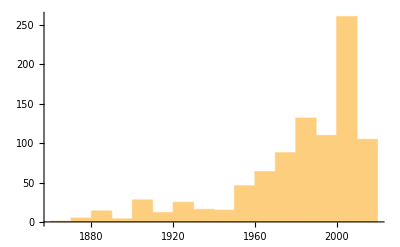

```mathematica
Histogram[Normal[Values[cites[All,"pubdate",1]]]]
```

## Join information from both datasets into association

Create an association by joining information from both datasets using DOI as primary key

```mathematica
doiAssoc1=JoinAcross[Normal@Values@cites[All,{"doi","pubdate"}],Normal@Values@keyterms[All,{"doi","keyterms"}],Key["doi"]]
```

{1}
 |  |  |  |

```mathematica
Head[doiAssoc1]
```

List

```mathematica
Head[First[doiAssoc1]]
```

Association

Keywords for records published in 1917

```mathematica
Cases[Normal@doiAssoc1,{_,"pubdate"->{1917,_,_},_}]
```

{{doi→10.2307/41347321,pubdate→{1917,5,25},keyterms→{engine→2.0,darwin→1.996,steam→1.989,papin→1.989,botanic→1.983,technics→1.982,eruditorum→1.981,lunar→1.98,lunars→1.979,gunpowder→1.978,colbert→1.978,garden→1.978,diver→1.977,submarine→1.977,erasmus→1.977,acta→1.976,borelli→1.976,goethe→1.976,boulton→1.975,piston→1.975,suggestion→1.975,note→1.975,motor→1.975,schiller→1.974,technical→1.974}},{doi→10.2307/20025723,pubdate→{1917,10,1},keyterms→{engine→2.0,calumet→1.986,hecla→1.984,steam→1.982,hoist→1.981,design→1.981,wheel→1.98,mechanical→1.98,cambridgeport→1.979,construction→1.978,engineer→1.977,retirement→1.977,consult→1.977,gallon→1.977,install→1.977,diameter→1.977,engineering→1.977,serve→1.977,equipment→1.977,cylinder→1.977,efficiency→1.976,stamp→1.976,twenty→1.976,expert→1.976,machine→1.976}}}

```mathematica
Keys[First[doiAssoc1]["keyterms"]]
```

{darwin,darwinism,darwinian,literary,levine,peckham,scholar,chicago,evolution,huxley,famou,century,nineteenth,science,perhap,literature,origin,lightman,desmond,gowan,secord,culture,natural,popularizer,gender}

```mathematica
MemberQ[Keys[First[doiAssoc1]["keyterms"]],"gender"]
```

True

```mathematica
(MemberQ[Keys[doiAssoc1⟦#⟧["keyterms"]],"gender"]&)[1]
```

True

Can strip down the association

```mathematica
doiAssoc2={doiAssoc1⟦#⟧["pubdate"]⟦1⟧,Keys@doiAssoc1⟦#⟧["keyterms"]}&/@Range[Length[doiAssoc1]];
```

Keys::invrl: The argument XMLElement["keyterm", {"weight" → ""}, {}] is not a valid Association or a list of rules.

General::stop: Further output of Keys :: invrl will be suppressed during this calculation.

```mathematica
Short[doiAssoc2,10]
```

{{2009,{darwin,darwinism,darwinian,literary,levine,peckham,scholar,chicago,evolution,huxley,famou,century,nineteenth,science,perhap,literature,origin,lightman,desmond,gowan,secord,culture,natural,popularizer,gender}},«924»,{1960,{darwin,evolutionary,lamarck,wilkie,marl,buffon,chapter,haldane,darwinism,selection,origin,natural,evolutionist,specie,whitehouse,animal,paleontological,galileo,extremely,centennial,particularly,fossil,survey,fertilization,character}}}

## Keyterms per year

Compute total number of keyterms per year - note increased numbers in 1909, 1959, 2009

```mathematica
keytermsPerYear=GroupBy[Sort[{#⟦1⟧,Length[#⟦2⟧]}&/@doiAssoc2],First->Last,Total]
```

<|1866→25,1874→50,1875→24,1877→47,1881→85,1882→76,1883→18,1885→38,1888→25,1895→50,1897→24,1899→25,1901→25,1906→23,1907→24,1908→50,1909→557,1910→46,1911→25,1912→48,1916→70,1917→50,1918→11,1919→21,1921→42,1922→24,1923→25,1924→50,1925→39,1926→89,1927→111,1928→67,1929→99,1931→21,1933→24,1934→50,1935→37,1936→62,1937→70,1938→60,1939→24,1941→24,1942→25,1943→24,1945→112,1946→25,1947→70,1948→62,1950→122,1951→49,1952→43,1954→49,1955→49,1956→23,1957→49,1958→194,1959→534,1960→333,1961→144,1962→195,1963→124,1964→153,1965→231,1966→80,1967→24,1968→116,1969→94,1970→146,1971→172,1972→147,1973→197,1974→346,1975→244,1976→147,1977→297,1978→193,1979→223,1980→238,1981→291,1982→692,1983→146,1984→194,1985→308,1986→315,1987→319,1988→320,1989→272,1990→288,1991→308,1992→341,1993→172,1994→239,1995→310,1996→294,1997→247,1998→230,1999→193,2000→143,2001→470,2002→567,2003→566,2004→423,2005→597,2006→596,2007→548,2008→447,2009→2002,2010→950,2011→822,2012→547,2013→141,2014→2|>

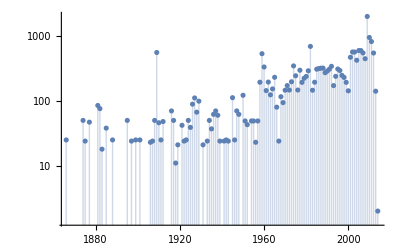

```mathematica
ListLogPlot[Reverse[keytermsPerYear],Filling->Axis,PlotRange->Full]
```

Make a structure that has keyterm over time as proportion of articles in which it appears

```mathematica
doiAssoc3=GroupBy[Flatten[Tuples[{doiAssoc2⟦#,2⟧,{doiAssoc2⟦#,1⟧}}]&/@Range[Length[doiAssoc2]],1],First->Last,Tally];
```

```mathematica
Short[doiAssoc3,10]
```

<|darwin→{{2009,71},{2006,19},{2012,22},{2004,15},{1916,2},{2010,38},{1992,14},{2003,22},{2005,19},{1909,18},{1975,9},{1988,11},{1978,8},{2011,33},{1971,7},{1986,10},{1921,2},{2007,20},{1958,7},{1881,3},{1965,9},{1908,2},{1982,28},{1899,1},{1995,11},{1994,7},{1993,7},{1964,7},{1959,15},{1928,3},{2002,17},{1999,8},{1926,3},{2008,10},{1973,6},{1980,9},{1924,2},{1989,9},{1957,2},{1952,2},{2001,16},«30»,{1983,7},{1897,1},{1895,2},{1972,5},{1910,2},{1969,3},{1950,5},{1997,9},{1931,1},{1998,9},{2000,6},{1991,7},{1938,2},{1901,1},{1956,1},{1943,1},{1963,3},{1951,2},{1966,4},{1955,2},{1939,1},{1937,3},{1883,2},{1877,2},{1911,1},{1874,2},{1912,2},{1866,1},{1935,2},{1875,1},{1923,1},{1922,1},{1917,1},{1885,2},{1933,1},{1946,1},{1888,1},{1941,1},{1967,1},{1907,1}},«6351»,…y→«1»|>

```mathematica
doiAssoc3["gender"]
```

{{2009,1},{2011,1},{2007,1},{2004,2}}

```mathematica
List[List[#⟦1⟧],#⟦2⟧]&/@doiAssoc3["huxley"]
```

{{{2009},7},{{1975},1},{{1995},4},{{2005},1},{{2010},9},{{1973},1},{{1980},1},{{1965},5},{{1981},2},{{1976},1},{{1927},2},{{2002},4},{{1928},1},{{1974},1},{{1909},2},{{2006},4},{{1999},1},{{1996},2},{{1982},3},{{1958},1},{{1926},1},{{2007},1},{{2001},2},{{1990},2},{{2011},3},{{1963},1},{{1951},1},{{1992},2},{{1985},1},{{1960},3},{{1961},1},{{1874},1},{{1959},3},{{1866},1},{{2000},1},{{1977},1},{{1984},2},{{1993},1},{{1875},1},{{2003},2},{{1972},1},{{1936},1},{{1922},1},{{1966},1},{{1962},1},{{2012},1},{{1994},1},{{1991},1},{{1998},1}}

Get frequencies for all keyterms

```mathematica
keytermFreq=SortBy[Tally[Flatten[Keys[doiAssoc1⟦#⟧["keyterms"]]&/@Range[Length[doiAssoc1]]]],Last];
```

Keys::invrl: The argument XMLElement["keyterm", {"weight" → ""}, {}] is not a valid Association or a list of rules.

General::stop: Further output of Keys :: invrl will be suppressed during this calculation.

```mathematica
Take[keytermFreq,-100]
```

{{rdquo,24},{reader,24},{religious,24},{galapagos,25},{life,25},{writing,25},{belief,26},{ethic,26},{hypothesis,26},{inheritance,26},{mdash,26},{variety,26},{work,26},{adaptation,27},{autobiography,27},{design,27},{experiment,27},{father,27},{fitzroy,27},{museum,27},{paley,27},{book,28},{concept,28},{creation,28},{spencer,28},{thought,28},{genetic,29},{sexual,29},{university,29},{moral,30},{evolutionist,31},{publish,31},{victorian,31},{earth,33},{historian,33},{change,34},{correspondence,34},{edition,34},{perhap,34},{population,34},{argument,36},{transmutation,37},{paper,38},{philosophy,38},{professor,38},{struggle,38},{theology,40},{biological,41},{island,41},{organic,41},{religion,41},{author,42},{fossil,42},{year,42},{world,43},{idea,44},{geological,45},{biology,47},{henslow,47},{principle,47},{hooker,49},{lamarck,49},{erasmus,50},{london,50},{geology,51},{naturalist,52},{essay,58},{malthus,58},{biologist,59},{descent,59},{cambridge,62},{variation,69},{chapter,70},{wallace,71},{organism,73},{scientist,80},{voyage,83},{write,83},{notebook,89},{plant,92},{huxley,93},{nature,105},{human,110},{lyell,115},{animal,117},{letter,124},{darwinism,136},{science,138},{beagle,157},{scientific,167},{charles,172},{darwinian,172},{evolutionary,228},{theory,241},{origin,245},{selection,279},{natural,307},{evolution,310},{specie,406},{darwin,797}}